# Numerical simulations in log-lin system

“Unilateral Tax Policy in the Open Economy”
by Miriam Kohl & Philipp M. Richter
June, 2023

```mathematica
Clear[σ,k,ti,χi,χj,χ]
```

```mathematica
(*
Description: compiles figures 1 & 2 in Section 4 and figure A.1 in Appendix A.6
*)
```

## Definitions

### General definitions

```mathematica
ζ[σ_,k_]:=k/(k-(σ-1));
λi[σ_,k_,ti_]:=Simplify[(ζ[σ,k](σ-1))/(ζ[σ,k](σ-1)+1-ti)];
B[σ_,k_,χi_, χj_ ]:=(2+χi+χj)σ/(σ-1)-(1-χi χj)1/k;
αi[σ_,k_,ti_]:=Simplify[ti/(ti+(σ-1)/λi[σ,k,ti])];
γi[σ_,k_,ti_,χi_]:=Simplify[1/(1+k/(σ-1)(ζ[σ,k](σ-1)+1)/(ζ[σ,k](σ-1)+1-ti) 1/χi)];
```

```mathematica
tildeti[σ_,k_,χi_, χj_]:=(1+((1+χi)(1+χj))/B[σ,k,χi, χj ])^(-1);
```

### Elasticities w.r.t. ti

```mathematica
elaλi[σ_,k_,ti_]:=Simplify[(1-λi[σ,k,ti])ti/(1-ti)];
elaχi[σ_,k_,ti_,χi_,χj_]:= Simplify[ti/(1-ti)((1+χi)(1+χj))/B[σ,k,χi, χj] elaλi[σ,k,ti]];
elarealwi[σ_,k_,ti_,χi_,χj_]:=-1/(1-ti)elaλi[σ,k,ti]+1/k χi/(1+χi)elaχi[σ,k,ti,χi,χj];
elarealRi[σ_,k_,ti_,χi_,χj_]:=elarealwi[σ,k,ti,χi,χj]+elaλi[σ,k,ti];
elarealbi[σ_,k_,ti_,χi_,χj_]:=1-ti/(1-ti)elaλi[σ,k,ti]+1/k χi/(1+χi)elaχi[σ,k,ti,χi,χj];
elarealmininci[σ_,k_,ti_,χi_,χj_]:=elarealwi[σ,k,ti,χi,χj]+αi[σ,k,ti](1+elaλi[σ,k,ti]);
elarealymini[σ_,k_,ti_,χi_,χj_]:=elarealRi[σ,k,ti,χi,χj]+(σ-1)/k αi[σ,k,ti];
elarealyminwototi[σ_,k_,ti_,χi_,χj_]:=-ti/(1-ti)elaλi[σ,k,ti]+(σ-1)/k αi[σ,k,ti];
elarealymintoti[σ_,k_,ti_,χi_,χj_]:=1/k χi/(1+χi)elaχi[σ,k,ti,χi,χj];
elaΞauti[σ_,k_,ti_]:=Simplify[-((ζ[σ,k]-1)ti)/(ζ[σ,k](σ-1)+1+(ζ[σ,k]-1)ti)];
elaΞopensymi[σ_,k_,ti_,χi_,χj_]:=Simplify[elaΞauti[σ,k,ti]+γi[σ,k,ti,χi](-elaλi[σ,k,ti])];
elaΞpureopeni[σ_,k_,ti_,χi_,χj_]:=Simplify[γi[σ,k,ti,χi](-elaλi[σ,k,ti])];
elaΞtoti[σ_,k_,ti_,χi_,χj_]:=γi[σ,k,ti,χi](elaχi[σ,k,ti,χi,χj]);
elaΞi[σ_,k_,ti_,χi_,χj_]:=Simplify[elaΞauti[σ,k,ti]+γi[σ,k,ti,χi](-elaλi[σ,k,ti]+elaχi[σ,k,ti,χi,χj])];
elaΩi[σ_,k_,ti_,χi_,χj_]:=1/(1+χi)elaχi[σ,k,ti,χi,χj];
elaΩj[σ_,k_,ti_,χi_,χj_]:=-1/(1+χj)elaχi[σ,k,ti,χi,χj];
elawi[σ_,k_,ti_,χi_,χj_]:=(σ/(σ-1)-1/k)^(-1)(1/k elaχi[σ,k,ti,χi,χj]-(1/(σ-1)-1/k)ti/(1-ti));
elaRi[σ_,k_,ti_,χi_,χj_]:=elawi[σ,k,ti,χi,χj]+elaλi[σ,k,ti];
elaPi[σ_,k_,ti_,χi_,χj_]:=elawi[σ,k,ti,χi,χj] +1/(1-ti)elaλi[σ,k,ti]-1/k χi/(1+χi)elaχi[σ,k,ti,χi,χj];
elarealRitot[σ_,k_,ti_,χi_,χj_]:=1/k χi/(1+χi)elaχi[σ,k,ti,χi,χj];
elarealRiλ[σ_,k_,ti_]:=-ti/(1-ti)elaλi[σ,k,ti];
elatoti[σ_,k_,ti_,χi_,χj_]:=1/k elaχi[σ,k,ti,χi,χj];
```

## Section 4 “Unilateral tax policy reform”

### Figure 1: Decomposed elasticity of minimum income w.r.t. the domestic tax rate

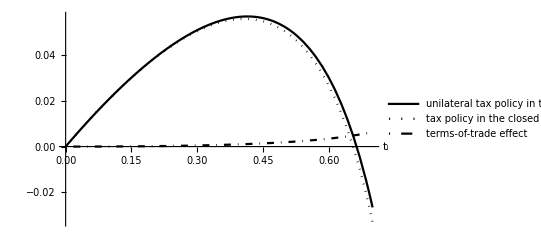

```mathematica
Clear[τ,σ,k,χ]
τ=1.27; σ=3.8;k=4;χ=τ^(-k);
figure1=Plot[{elarealymini[σ,k,ti,χ,χ],elarealyminwototi[σ,k,ti,χ,χ],elarealymintoti[σ,k,ti,χ,χ]},{ti,0,0.7},
PlotStyle->{{Black},{Black,Dotted},{Black,DotDashed},{Black,Dashed}},AxesLabel->{Style[Subscript[t, i],FontSize->10]},
PlotLegends->Placed[LineLegend[{Style["unilateral tax policy in the open economy",FontSize->12],Style["tax policy in the closed economy/\nsymmetric tax policy in the open economy",FontSize->12],Style["terms-of-trade effect",FontSize->12]}],Right]]
Export["UnilateralTax_Figure_1.pdf",figure1];
Clear[τ,σ,k,χ]
```

### Figure 2: Decomposed elasticity of inter-group inequality w.r.t. the domestic tax rate

0.948152

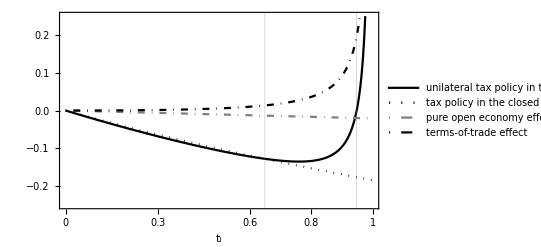

```mathematica
Clear[τ,σ,k,χ]
τ=1.27; σ=3.8;k=4;χ=τ^(-k);
rootti=Part[FindRoot[{elaΞi[σ,k,ti,χ,χ]==0},{{ti,0.8}}]][[;;,2]][[1]]
figure2=Plot[{elaΞi[σ,k,ti,χ,χ],elaΞauti[σ,k,ti],elaΞpureopeni[σ,k,ti,χ,χ],elaΞtoti[σ,k,ti,χ,χ]
},{ti,0,1},
PlotStyle->{{Black},{Black,Dotted},{Gray,DotDashed},{Black,DotDashed}},PlotLegends->Placed[LineLegend[{Style["unilateral tax policy in the open economy",FontSize->12],Style["tax policy in the closed economy",FontSize->12],Style["pure open economy effect", FontSize->12],Style["terms-of-trade effect",FontSize->12]}],Right],
GridLines->{{rootti,tildeti[σ,k,χ, χ]}},
Frame-> {{True,False},{True,False}}, 
FrameLabel->{Style[Subscript[t, i],FontSize->10]},
FrameTicks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,{tildeti[σ,k,χ, χ],OverTilde[Subscript[t, i]]},0.7,.8,.9,{rootti,OverDot[Subscript[t, i]]},1},Automatic},
PlotRange->{{0,1},{-0.25,0.25}}
]
Export["UnilateralTax_Figure_2.pdf",figure2];
Clear[τ,σ,k,χ]
```

## Appendix A.6 “The role of k and σ on the effect on the terms of trade in Eq. (25)”

### Figure A1: The role of k and σ for the elasticity of country-i’s terms of trade w.r.t. the domestic tax rate given the initial tax ti = tj = t.

0.147765

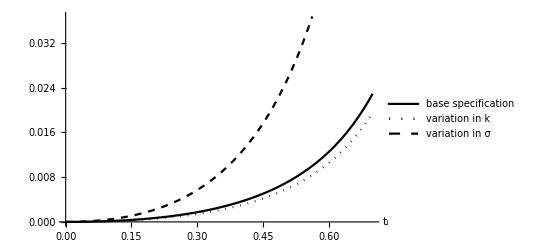

```mathematica
Clear[τ,σ,χ]
τ=1.27; χk4=τ^(-4);χk8=τ^(-8)
figureA1=Plot[{elatoti[3.8,4,ti,χk4,χk4],elatoti[3.8,8,ti,χk8,χk8],elatoti[2,4,ti,χk4,χk4]},{ti,0,0.7},
PlotStyle->{{Black},{Black,Dotted},{Black,Dashed}},AxesLabel->{Style[Subscript[t, i],FontSize->10]},
PlotLegends->Placed[LineLegend[{Style["base specification",FontSize->12],Style["variation in k",FontSize->12],Style["variation in σ",FontSize->12]}],Right]]
(*PlotLegends->Placed[LineLegend[{Style["Base specification",FontSize->12],Style["Variation in k (k=8)",FontSize->12],Style["Variation in σ (σ=2)",FontSize->12]}],Right]]*)
Export["UnilateralTax_Figure_A1.pdf",figureA1];
```